TO DO:
Play with opacity w/ shells
Add equipotential lines to energy diagrams

Add rf lines to bare potential.

LABELS!

```mathematica
(* Send to the right directory if necessary *)
(* the main project directory sits one above this subproject directory, i.e. at the -2 position. *)
projectDirectory=FileNameTake[NotebookDirectory[],{1,-2}]
packageDirectory=FileNameJoin@{projectDirectory,"mathematica_packages\\"}
outputDirectory=FileNameJoin@{projectDirectory,"output\\"}

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]

Get["SMThreeChipModel.m"]
Get["SMThreeTraps.m"]
```

C:\Users\josep\forschung\modeling\bubble_bec

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

## Define fields

```mathematica
(*bFieldTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*{x^2,y^2,z^2};*)
(*bFieldMagTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*Sqrt[x^4+y^4+z^4];*)

anisotropy=1.1;
bFieldMagTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*(x^2+(y/anisotropy)^2+z^2);

b0TOY=5.*Gauss;(* G *)
omegaTrap = (2.*Pi)*20.0;(* rad/s *)
mF=1;
bCurveTOY=mRb*omegaTrap^2/(2.*mF*gF*μB )(* 1.5*10^4 *)(*T/m^2*)

(* added small non-zero energy (10 Hz) in order to help the program consistently define the upper and lower energies. Otherwise plots are filled in between the curves as each solution jumps from the higher to lower energy band rapidly. *)
xCor=1./Sqrt[2.]; (* was 1 *)
hamiltonianTOY[Δ_,Ω_,x_,y_,z_]:=({{Δ,xCor*Ω/2,0},{xCor*Ω/2,0,xCor*Ω/2},{0,xCor*Ω/2,-Δ}}+{{#[[2]],0,0},{0,10,0},
{0,0,-#[[2]]}}&[ZeemanShiftC@bFieldMagTOY[b0TOY,bCurveTOY,x,y,z]]);

(*
(* w/ quadratic Zeeman shift *)
hamiltonianTOY[Δ_,Ω_,x_,y_,z_]:=({{Δ,xCor*Ω/2,0},{xCor*Ω/2,0,xCor*Ω/2},{0,xCor*Ω/2,-Δ}}+{{#[[2]],0,0},{0,#[[3]]/100000,0},
{0,0,#[[4]]}}&[ZeemanShiftC@bFieldMagTOY[b0TOY,bCurveTOY,x,y,z]]);
*)

adiabaticEnergiesTOY[Δ_,Ω_,x_,y_,z_]:=Eigenvalues@hamiltonianTOY[Δ,Ω,x,y,z];
adiabaticEnergyStatesTOY[Δ_,Ω_,x_,y_,z_]:=Eigenvectors@hamiltonianTOY[Δ,Ω,x,y,z];
maxAdiabaticEnergyTOY[Δ_,Ω_,x_,y_,z_]:=Max@Eigenvalues@hamiltonianTOY[Δ,Ω,x,y,z];
```

245.815

## Plot spins

3.49253×10^6

3.53661×10^6

xMax (um) = 300.

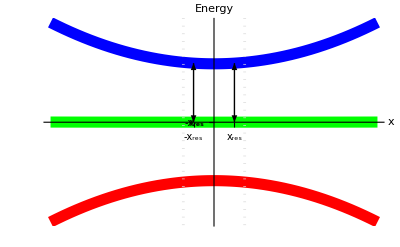

```mathematica
energySplitting=(ZeemanShift[b0TOY]//Differences)[[4]](* Hz *)
(*cdetuning=bCurveTOY*μB*(500*10^(-6))^2/(hbar*2*Pi)*)
xPotMin=150.; (* um *) (* Set to match the population plots *)
cDelta=gF*μB*(b0TOY+bCurveTOY*(xPotMin*10^(-6))^2)/h
(*cDelta=(*4**)(*2**)energySplitting+50*^3; (* Hz *)*)
cOmega=(*(*Model*)(2*Pi)*)17.*1*^3; (* Hz *)
(*xPotMin=Sqrt[(hbar*2*Pi*cDelta-gF*μB*b0TOY)/(gF*μB*bCurveTOY)]*10^6;*) (* um *)
xMax= 2.*xPotMin;(* um *)
xMin=-xMax;
xStp=(xMax-xMin)/200;

Print["xMax (um) = "<>ToString@xMax];

(*
(*WORKING:*)
cDelta=(*4**)2*energySplitting+1.7*^6; (* Hz *)
cOmega=(*(*Model*)(2*Pi)*)100*1*^3; (* Hz *)
xMax=10^3; (* um *)
xMin=-xMax;
xStp=(xMax-xMin)/200;
*)

defaultPlotOptions=Options[Plot];

myPlotOptions={
ColorFunctionScaling->False, (* Necessary for our user-defined functions for the plots' line colors to work. *)
(* Aesthetics: *)
PlotStyle->Thickness[0.02],
PlotRange->All,
AxesOrigin->{0,0},
AxesStyle->Directive[{Thickness[0.01],Arrowheads[Automatic]}],
AxesLabel->{Automatic,"Energy"},
Ticks->{{{-xPotMin,"-x_res"},{xPotMin,"x_res"}}},
TicksStyle->None
};

SetOptions[Plot,myPlotOptions];

Block[
{energies,
curveColors=RGBColor/@{{1,0,0},{0,1,0},{0,0,1}}(*These triplets define the RGB colors for each of the bare states, -1 (red), 0 (green), and 1 (blue), respectively.*),
plot, legend,
rangeMult=4,
arSz=0.05 (* size of arrow heads *)
},

energies[x_]:=ZeemanShiftC[bFieldMagTOY[b0TOY,bCurveTOY,x*10^(-6),0,0]][[{1,3,5}]];

plot=Show[
Plot[energies[x][[#]],{x,rangeMult*xMin,rangeMult*xMax},
ColorFunction->Function[{x,y},curveColors[[#]]],
GridLines->{{0.75*xMin,0.75xMax},{}},
GridLinesStyle->Directive[Dotted,Thickness[0.005]],
(* resonance arrows *)
Epilog->{
{Arrowheads[{-arSz,arSz}],Arrow[{{-xPotMin,0},{-xPotMin,energies[xPotMin][[3]]}}]},(*,
{Arrowheads[{-arSz,arSz}],Arrow[{{-xPotMin,0},{-xPotMin,energies[xPotMin][[1]]}}]}*),
{Arrowheads[{-arSz,arSz}],Arrow[{{xPotMin,0},{xPotMin,energies[xPotMin][[3]]}}]}
}
]&/@{1,2,3}
];

legend=LineLegend[Reverse@curveColors,{"1","0","-1"}];

(*energiesBarePlot=Legended[plot,legend];*)
energiesBarePlot=plot
]
```

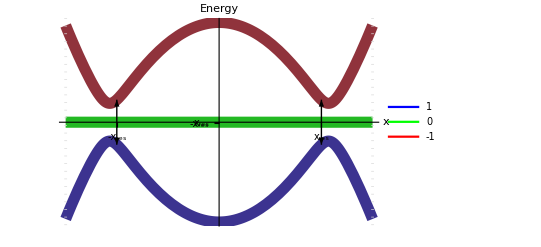

```mathematica
Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,arSz=0.04},

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,0.75*xMin,0.75*xMax},
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
GridLines->{{0.75*xMin,0.75*xMax},{}},
GridLinesStyle->Directive[Dotted,Thickness[0.005]],
Epilog->{
{Arrowheads[{-arSz,arSz}],Arrow[{{-xPotMin,-energies[xPotMin][[1]]},{-xPotMin,energies[xPotMin][[1]]}}]},
{Arrowheads[{-arSz,arSz}],Arrow[{{xPotMin,-energies[xPotMin][[1]]},{xPotMin,energies[xPotMin][[1]]}}]}
}
]&/@{1,2,3}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;

Legended[plot,legend]
]
```

-Graphics3D-

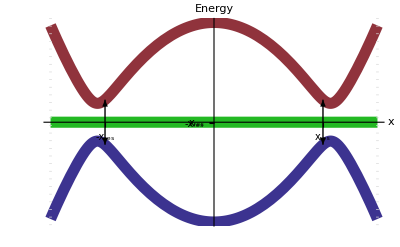
-Graphics- | -Graphics3D- | -Graphics-

```mathematica
defaultContourPlot3DOptions=Options[ContourPlot3D];
myContourPlot3DOptions={
RegionFunction->Function[{x,y,z},x<0||y>0||z<0], (* creates cross-section *)
RegionBoundaryStyle->None,
Ticks->None,
(*Boxed->False,*)
(*AxesOrigin->{0,0,0},*)
(*AxesStyle->Thickness[0.01],*)
AxesLabel->{"x","y","z"}
};

SetOptions[ContourPlot3D,myContourPlot3DOptions];

Block[{sphere,maxBound=1},
sphere[x_,y_,z_]:=x^2+y^2+z^2;

spinLegend=ContourPlot3D[
{sphere[x,y,z]==1(*,sphere[x,y,z]==3,sphere[x,y,z]==9*)},
{x,0,maxBound},{y,0,maxBound},{z,0,maxBound},
ColorFunction->Function[{x,y,z},RGBColor@{x,y,z}],
ContourStyle->Opacity[1],
Mesh->False,
BoxStyle->None,
AxesOrigin->{0,0,0},
AxesLabel->{"m=-1","m=0","m=1"},
Axes->True,
Boxed->False,
ViewPoint->({#,#,#}&[5]),
Lighting->{"Ambient",White},
PlotLabel->"Spin composition"]
]

SetOptions[ContourPlot3D,defaultContourPlot3DOptions];

spinGrid=Grid@{{energiesBarePlot,spinLegend,energiesDressedPlot}}

SetOptions[Plot,defaultPlotOptions];
```

## Plot energies

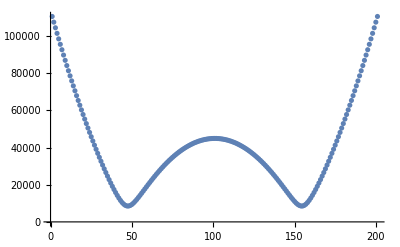

Min = 0.008538 MHz

Max = 0.237835 MHz

Min loc = -0.000156

```mathematica
numEnergies=Table[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]],{x,xMin,xMax,xStp}];
ListPlot@numEnergies
approxMin=Min@numEnergies;
Print["Min = "<>ToString[%*10^(-6)]<>" MHz"];
plotMax=adiabaticEnergiesTOY[cDelta,cOmega,xMax*10^(-6),xMax*10^(-6),0][[1]];
Print["Max = "<>ToString[%*10^(-6)]<>" MHz"];
plotRange=(plotMax-approxMin);
(minLoc=(Ordering[numEnergies,1][[1]]*xStp-xMax)*10^(-6))//N;
Print["Min loc = "<>ToString@%];
```

```mathematica
approxMin
plotRange
colorFunc[v_]:=(ColorData["SolarColors"][1.5*(v-approxMin)/plotRange]);
colorFunc[approxMin]
colorFunc[v_]:=Module[
{f=Log@(#)&,range,min,max},
min = f[approxMin];
max=f[plotMax];
range=max-min;
Return[(ColorData["SolarColors"][(f[v]-min)/range])];
];
```

8538.

229297.

RGBColor[0.468742, 0., 0.0158236]

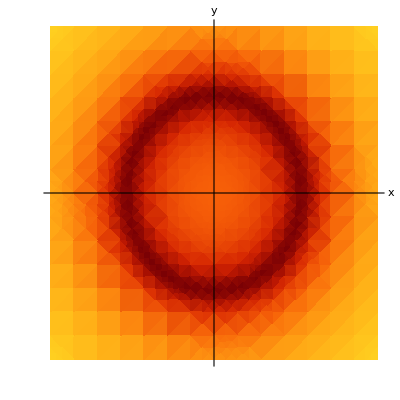

```mathematica
plotPot2d=DensityPlot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),0][[1]],
{x,xMin,xMax},{y,xMin,xMax},
ColorFunction->(colorFunc[#1]&),
ColorFunctionScaling->False,
Frame->False,
Axes->True,
Ticks->False,
AxesStyle->Directive[{Thickness[0.01],Arrowheads[Automatic]}],
AxesLabel->Automatic(*,
MaxRecursion->4*)
]
```

29374.6

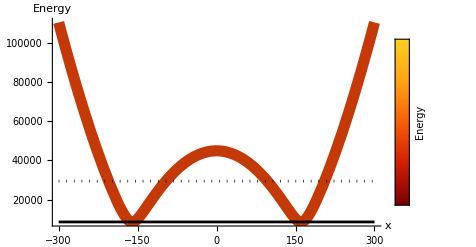

```mathematica
SetOptions[Plot,myPlotOptions];
maxPotCen=Sqrt[(cDelta-energySplitting)^2+(cOmega/2)^2];

temperature=200*10^(-9);(* [K] *)
hotVal=5*kb*temperature/h+approxMin
secLineVal=hotVal;
Block[
{
minLine={Thickness[0.005],Line[{{xMin,approxMin},{xMax,approxMin}}]},
hotLine={Dashed,Thickness[0.005],Red,Line[{{xMin,hotVal},{xMax,hotVal}}]},
maxLine={Dotted,Thickness[0.005],Line[{{xMin,secLineVal},{xMax,secLineVal}}]}
},
plotPot1d=Legended[
Plot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]],{x,xMin,xMax},
ColorFunction->(colorFunc[#2]&),
ColorFunctionScaling->False(*,
Frame->True,
Axes->False*),
Ticks->True,
Epilog->{minLine,maxLine(*,hotLine*)}],
BarLegend["SolarColors",Ticks->None,LegendLabel->"Energy"]
]
]

SetOptions[Plot,defaultPlotOptions];
```

```mathematica
ContourPlot[{
adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),0][[1]]==approxMin,
adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),0][[1]]==secLineVal},
{x,xMin,xMax},{y,xMin,xMax},
(*ColorFunction->(colorFunc[#1]&),
ColorFunctionScaling->False,*)
ContourStyle->{{Black(*,Dashed*),Thickness[0.005]},{Black,Dotted,Thickness[0.005]}},
Frame->False,
Axes->True,
Ticks->False,
AxesStyle->Directive[{Thickness[0.01],Arrowheads[Automatic]}],
AxesLabel->Automatic,
Mesh->All,
MaxRecursion->7
]
plotPot2dFinal=Show@{plotPot2d,%}
```

CompiledFunction::cfsa: Argument 0.0005+245.815 (x^2/1000000000000+8.26446×10^-13 y^2) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

-Graphics-

-Graphics-

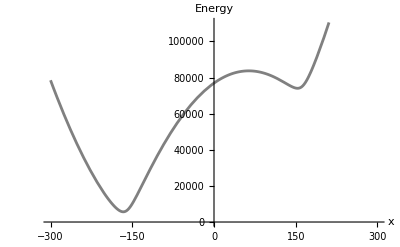

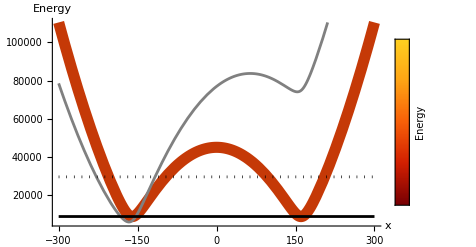

```mathematica
SetOptions[Plot,myPlotOptions];

(*Legended[
Plot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]+9.8*mRb*(x*10^(-6))/(2*Pi*hbar),{x,xMin,xMax},
ColorFunction->(colorFunc[#2]&),
ColorFunctionScaling->False,
Ticks->True],
BarLegend["SolarColors",Ticks->None,LegendLabel->"Energy"]
]*)

gravPotential[x_,gFrac_]:=gFrac*9.8*mRb*x/h;

Module[{scale=1/20,energy,offset},
offset=-((gravPotential[#,0.1])&[-xPotMin*10^(-6)]);
energy[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]];
gravPlot=Plot[
(energy[x]+gravPotential[x*10^(-6),0.1]+offset),
{x,xMin,xMax},
PlotRange->{0,energy[xMax]},
PlotStyle->{Gray,Thickness[0.005]},
(*ColorFunction->(colorFunc[#2]&),*)
ColorFunctionScaling->False,
Ticks->True]
]

plotPot1d=Show@{plotPot1d,gravPlot}

SetOptions[Plot,defaultPlotOptions];
```

```mathematica
(*Block[{energy,contourStyles,minEnergyOffset=0.15*^6,secondSurfaceOffset=5*^6},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});

(*Print[contourStyles];*)

plotPot3d=ContourPlot3D[
{energy[x,y,z]==approxMin+minEnergyOffset,energy[x,y,z]==approxMin+secondSurfaceOffset},
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
(*PlotPoints->10,
MaxRecursion->4,*)
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->{ColorData["SolarColors"][0],ColorData["SolarColors"][1]},
RegionBoundaryStyle->None]
]*)
```

```mathematica
Block[{energy,contourStyles,minEnergyOffset=0.5*^3(*,secondSurfaceOffset=5*^6*),opacity=0.2},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});
Print["Min [kHz] = "<>ToString[approxMin/10^3]];
Print["Plotted min [kHz] = "<>ToString[(approxMin+minEnergyOffset)/10^3]];
Print["Seclineval [kHz] = "<>ToString[secLineVal/10^3]];
plotPot3dMin=ContourPlot3D[
energy[x,y,z]==approxMin+minEnergyOffset,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},(x<0||y>0||z<0)&&(x^2+(y/anisotropy)^2+z^2>((minLoc*10^6)^2))],
ContourStyle->colorFunc[approxMin],
RegionBoundaryStyle->None(*,
WorkingPrecision->20*),
MaxRecursion->1,
PlotPoints->40];

(*plotPot3dOuter=ContourPlot3D[
energy[x,y,z]==secLineVal,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->{colorFunc[secLineVal],Opacity[opacity]},
MeshStyle->Opacity[opacity],
RegionBoundaryStyle->None];*)

Show@{plotPot3dMin(*,plotPot3dOuter*)}

]
```

Min [kHz] = 8.50509

Plotted min [kHz] = 9.00509

Seclineval [kHz] = 29.3417

CompiledFunction::cfsa: Argument 0.0005+245.815 (x^2/1000000000000+8.26446×10^-13 y^2+z^2/1000000000000) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

-Graphics3D-

```mathematica
Block[{energy,contourStyles,opacity=0.5,minEnergyOffset=0.15*^6,secondSurfaceOffset=4*^6},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});

(*Print[contourStyles];*)

plotPot3dOuter=ContourPlot3D[
energy[x,y,z]==secLineVal,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->{colorFunc[secLineVal],Opacity[opacity]},
MeshStyle->Opacity[opacity],
RegionBoundaryStyle->None]
]
```

CompiledFunction::cfsa: Argument 0.0005+245.815 (x^2/1000000000000+8.26446×10^-13 y^2+z^2/1000000000000) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotPot3d=Show[plotPot3dOuter,plotPot3dMin]
```

-Graphics3D-

```mathematica
energyGrid=Grid@{{
Show[plotPot1d,Ticks->False],
plotPot2dFinal,
Show[plotPot3d,Ticks->False,AxesLabel->{"x","y","z"}]}};
```

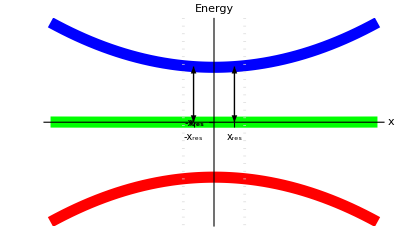
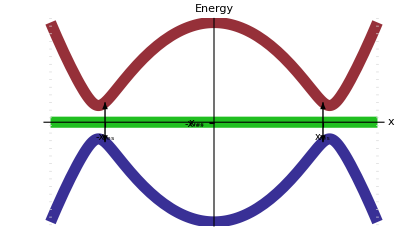
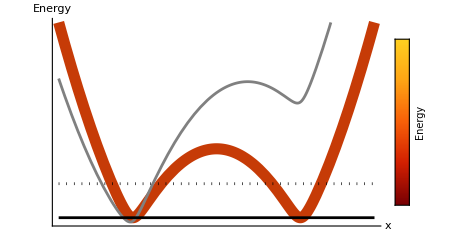
-Graphics- | -Graphics3D- | -Graphics-
-Graphics- | -Graphics- | -Graphics3D-
atomGrid

```mathematica
Grid[{{spinGrid},{energyGrid},{atomGrid}},Frame->All]
```

Dressing a bubble in a toy spin F=1 model. The spin dependent force experienced by atoms in a quadratic magnetic field is modified by the introduction of an rf field. The potential can be derived by transforming the atomic bare state atomic Hamiltonian into a rotating frame wherein time-dependence is removed by performing the rotating wave approximation. An atom whose introduction to and movement through the resulting potential is sufficiently adiabatic remains in one of the resulting energy curves.

By detuning the rf field from resonance at the minimum of the m=1 curve, potential dips are created at the points where the field is resonant. Any straight path that passes through the origin will experience the potential dips on either side of the B field minimum. Thus the minimum of the dressed potential forms a shell in dimensions.

Atoms with sufficiently low energy will be trapped around this minimum and form a bubble-shaped cloud.

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"fig1draft3.jpeg"},Grid[{{spinGrid},{energyGrid},{atomGrid}},Frame->All]]
```

C:\Users\josep\forschung\modeling\bubble_bec\sm2_manuscript_figures\fig1draft3.jpeg

```mathematica
SetOptions[ContourPlot3D,myContourPlot3DOptions];

Block[{sphere,plot1,plot2},
sphere[x_,y_,z_]:=x^2+y^2+z^2;
ContourPlot3D[{sphere[x,y,z]==1,sphere[x,y,z]==3,sphere[x,y,z]==9},
{x,-3,3},{y,-3,3},{z,-3,3},
(*RegionFunction->Function[{x,y,z},x<0||y>0||z<0],*)
ContourStyle->({#[1],#[0],#[1]}&[ColorData["SolarColors"]])];

plot1=ContourPlot3D[
{sphere[x,y,z]==1(*,sphere[x,y,z]==3,sphere[x,y,z]==9*)},
{x,-3,3},{y,-3,3},{z,-3,3},
RegionFunction->Function[{x,y,z},(x<0||y>0||z<0)&&(x^2+y^2+z^2<1.1)],
ContourStyle->(colorFunc[#1]&)(*({#[1],#[0],#[1]}&[ColorData["SolarColors"]])*)];

plot2=ContourPlot3D[{(*sphere[x,y,z]==1,*)sphere[x,y,z]==9(*,sphere[x,y,z]==9*)},
{x,-3,3},{y,-3,3},{z,-3,3},
ContourStyle->{Opacity[0.2],(colorFunc[#1]&)}(*({#[1],#[0],#[1]}&[ColorData["SolarColors"]])*),
MeshStyle->{Opacity[0.2]}];

Show@{plot1,plot2}

]

SetOptions[ContourPlot3D,defaultContourPlot3DOptions];
```

-Graphics3D-

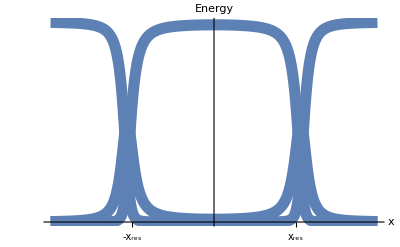

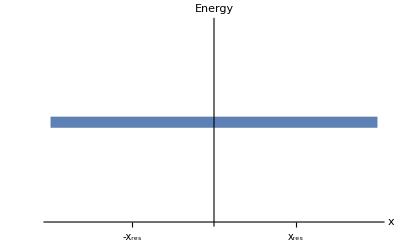

```mathematica
Plot[adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]^2,{x,xMin,xMax}]
Plot[Total@(#^2)&[adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]],{x,xMin,xMax}]
```

```mathematica
Options[ContourPlot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,1},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,Contours→Automatic,ContourStyle→GrayLevel[1],ControllerLinking→False,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&,#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionBoundaryStyle→Automatic,RegionFunction→(True&),RotationAction→Fit,SphericalRegion→Automatic,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

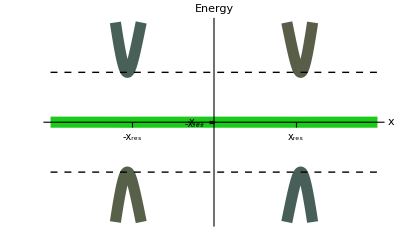

```mathematica
SetOptions[Plot,myPlotOptions];

Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,range=cOmega,xMin=xMin,xMax=xMax},

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},PlotRange->{-range,range},AxesOrigin->Automatic,
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
Epilog->{{Dashed,Line[{{xMin,0.5*cOmega},{xMax,0.5*cOmega}}]},
{Dashed,Line[{{xMin,-0.5*cOmega},{xMax,-0.5*cOmega}}]}}]&
/@{1,2,3}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;

Legended[plot,legend];
]

Show[energiesDressedPlot]

SetOptions[Plot,defaultPlotOptions];
(* Dashed line is Rabi freq/2 (cOmega/2) *)
```

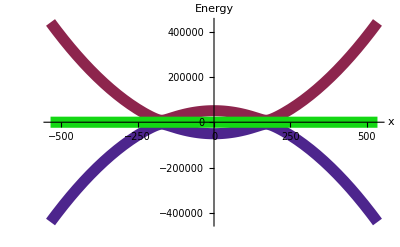

1014.72

```mathematica
SetOptions[Plot,myPlotOptions];
(*cDelta=energySplitting+200*^3;*)
Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,xMax=535,xMin},
xMin=-xMax;

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
Ticks->Automatic,PlotRange->All]&
/@{1,2,3}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;

Legended[plot,legend];
]

Show@energiesDressedPlot
(*Sqrt[hbar*cDelta*2*Pi/(2*mRb*omegaTrap^2)]*10^6*)
Sqrt[hbar*cDelta*2*Pi/(bCurveTOY*μB)]*10^6
SetOptions[Plot,defaultPlotOptions];
```

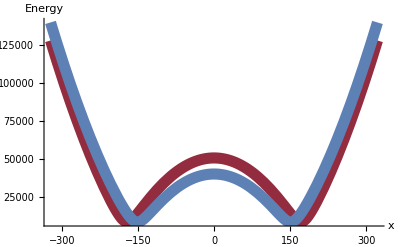

```mathematica
analyticPotential[Delta_,Omega_,x_,y_,z_]:=Module[
{r=Sqrt[x^2+y^2+z^2],fL0,fLr,fPot},
(*fL0=((ZeemanShiftC[b0TOY]//Differences)[[4]]//N);*)
fLr:=ZeemanShiftC[bFieldMagTOY[b0TOY,bCurveTOY,x,y,z]][[4]];
fPot=Sqrt[(cDelta(*+fL0*)-fLr)^2+(Omega/2)^2];
Return[fPot];
];

SetOptions[Plot,myPlotOptions];
(*cDelta=energySplitting+200*^3;*)
Block[
{energies,stateCompositionX,lineColorFunc,plot,legend,xMax=xMax,xMin},
xMin=-xMax;

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},
ColorFunction->Function[{x,y},lineColorFunc[x,#]],
Ticks->Automatic,PlotRange->All]&
/@{1}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;
analyticPlot=Plot[analyticPotential[cDelta,cOmega,x*10^(-6),0,0],{x,xMin,xMax}];

Legended[plot,legend];
]

Show[energiesDressedPlot, analyticPlot,PlotRange->All]


SetOptions[Plot,defaultPlotOptions];
```